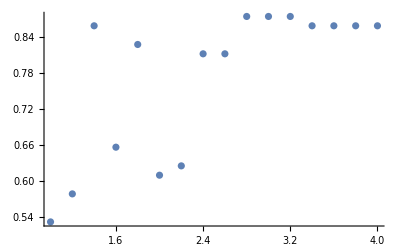

```mathematica
b={{1,(65-30-1)/64}, {1.2,(65-27-1)/64},{1.4,(65-9-1)/64},{1.6,(65-22-1)/64}, {1.8,(65-11-1)/64},{2,(65-25-1)/64},{2.2,(65-24-1)/64},{2.4,(65-12-1)/64},{2.6,(65-12-1)/64},{2.8,(65-8-1)/64},{3,(65-8-1)/64},{3.2,(65-8-1)/64},{3.4,(65-9-1)/64},{3.6,(65-9-1)/64},{3.8,(65-9-1)/64},{4,(65-9-1)/64}};
ListPlot[b]
```

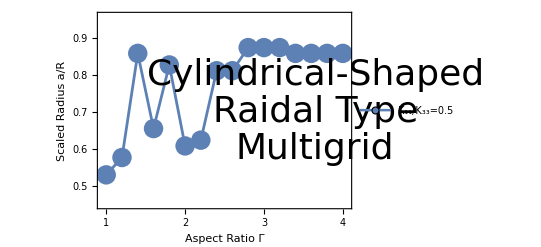

```mathematica
ListPlot[{b},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.5,0.6,0.7,0.8,0.9},None},{{1,2,3,4},None}}, PlotRange->{{0.95,4.05},{0.45,0.96}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.5"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Top}],Epilog->{Text[Style["Cylindrical-Shaped",Directive[Black,36]],{3.65,0.8}],Text[Style["Raidal Type",Directive[Black,36]],{3.65,0.7}],Text[Style["Multigrid",Directive[Black,36]],{3.65,0.6}]}]
```

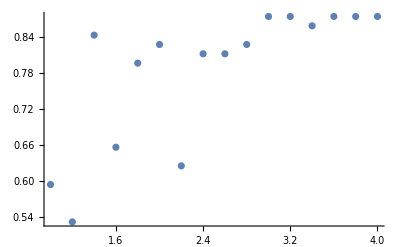

```mathematica
b2={{1,(65-26-1)/64}, {1.2,(65-30-1)/64},{1.4,(65-10-1)/64},{1.6,(65-22-1)/64}, {1.8,(65-13-1)/64},{2,(65-11-1)/64},{2.2,(65-24-1)/64},{2.4,(65-12-1)/64},{2.6,(65-12-1)/64},{2.8,(65-11-1)/64},{3,(65-8-1)/64},{3.2,(65-8-1)/64},{3.4,(65-9-1)/64},{3.6,(65-8-1)/64},{3.8,(65-8-1)/64},{4,(65-8-1)/64}};
ListPlot[b2]
```

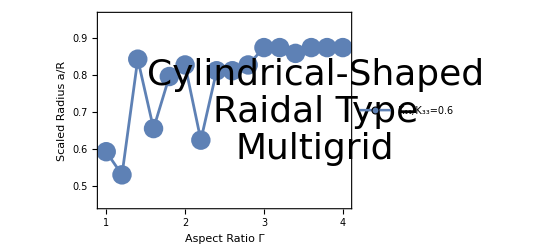

```mathematica
ListPlot[{b2},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.5,0.6,0.7,0.8,0.9},None},{{1,2,3,4},None}}, PlotRange->{{0.95,4.05},{0.45,0.96}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.6"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Top}],Epilog->{Text[Style["Cylindrical-Shaped",Directive[Black,36]],{3.65,0.8}],Text[Style["Raidal Type",Directive[Black,36]],{3.65,0.7}],Text[Style["Multigrid",Directive[Black,36]],{3.65,0.6}]}]
```

```mathematica
N[1/32,9]
```

0.03125

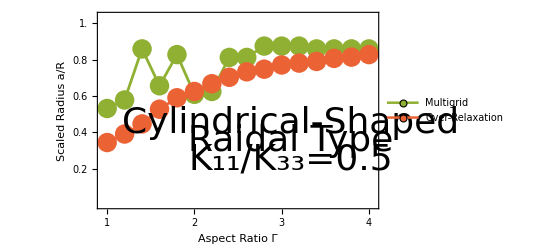

```mathematica
bb={{1,11/(32×1)}, {1.2,15/(32×1.2)},{1.4,20/(32×1.4)},{1.6,27/(32×1.6)}, {1.8,34/(32×1.8)},{2,40/(32×2)},{2.2,47/(32×2.2)},{2.4,54/(32×2.4)},{2.6,61/(32×2.6)},{2.8,67/(32×2.8)},{3,74/(32×3)},{3.2,80/(32×3.2)},{3.4,86/(32×3.4)},{3.6,93/(32×3.6)},{3.8,99/(32×3.8)},{4,106/(32×4)}};
ListPlot[{b,bb},PlotStyle->{{Thickness[0.005],RGBColor[0.560181,0.691569,0.194885]},{Thickness[0.005],RGBColor[0.922526,0.385626,0.209179]}},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.2,0.4,0.6,0.8,1.0},None},{{1,2,3,4},None}}, PlotRange->{{0.95,4.05},{0,1.04}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"Multigrid", "Over-Relaxation"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Bottom}],Epilog->{Text[Style["Cylindrical-Shaped",Directive[Black,36]],{3.1,0.45}],Text[Style["Raidal Type",Directive[Black,36]],{3.1,0.35}],Text[Style["K_11/K_33=0.5",Directive[Black,36]],{3.1,0.25}]}]
```

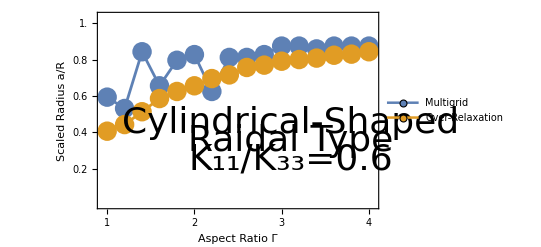

```mathematica
bb2={{1,13/(32×1)}, {1.2,17/(32×1.2)},{1.4,23/(32×1.4)},{1.6,30/(32×1.6)}, {1.8,36/(32×1.8)},{2,42/(32×2)},{2.2,49/(32×2.2)},{2.4,55/(32×2.4)},{2.6,63/(32×2.6)},{2.8,69/(32×2.8)},{3,76/(32×3)},{3.2,82/(32×3.2)},{3.4,88/(32×3.4)},{3.6,95/(32×3.6)},{3.8,101/(32×3.8)},{4,108/(32×4)}};
ListPlot[{b2,bb2},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.2,0.4,0.6,0.8,1.0},None},{{1,2,3,4},None}}, PlotRange->{{0.95,4.05},{0,1.04}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"Multigrid", "Over-Relaxation"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Bottom}],Epilog->{Text[Style["Cylindrical-Shaped",Directive[Black,36]],{3.1,0.45}],Text[Style["Raidal Type",Directive[Black,36]],{3.1,0.35}],Text[Style["K_11/K_33=0.6",Directive[Black,36]],{3.1,0.25}]}]
```

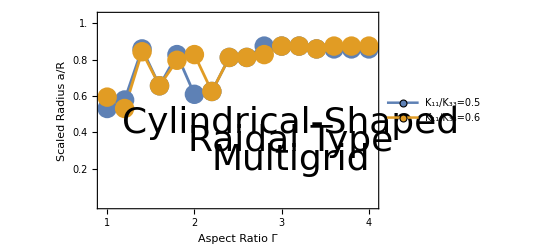

```mathematica
ListPlot[{b,b2},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.2,0.4,0.6,0.8,1.0},None},{{1,2,3,4},None}}, PlotRange->{{0.95,4.05},{0,1.04}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.5", "K_11/K_33=0.6"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Bottom}],Epilog->{Text[Style["Cylindrical-Shaped",Directive[Black,36]],{3.1,0.45}],Text[Style["Raidal Type",Directive[Black,36]],{3.1,0.35}],Text[Style["Multigrid",Directive[Black,36]],{3.1,0.25}]}]
```

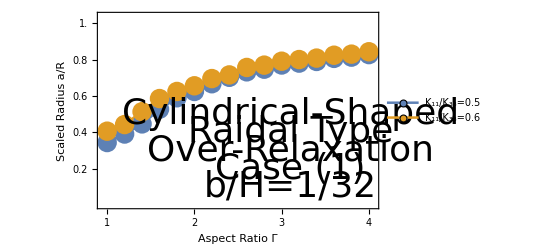

```mathematica
ListPlot[{bb,bb2},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.2,0.4,0.6,0.8,1.0},None},{{1,2,3,4},None}}, PlotRange->{{0.95,4.05},{0,1.04}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.5", "K_11/K_33=0.6"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Bottom}],Epilog->{Text[Style["Cylindrical-Shaped",Directive[Black,36]],{3.1,0.5}],Text[Style["Raidal Type",Directive[Black,36]],{3.1,0.4}],Text[Style["Over-Relaxation",Directive[Black,36]],{3.1,0.3}],Text[Style["Case (1)",Directive[Black,36]],{3.1,0.2}],Text[Style["b/H=1/32",Directive[Black,36]],{3.1,0.1}]}]
```

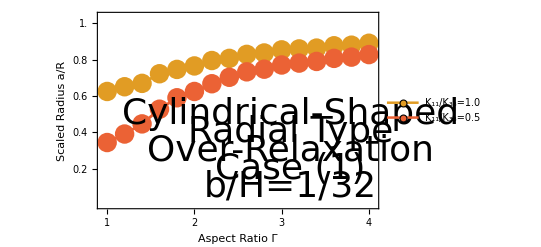

```mathematica
bb3={{1,20/(32×1)}, {1.2,25/(32×1.2)},{1.4,30/(32×1.4)},{1.6,37/(32×1.6)}, {1.8,43/(32×1.8)},{2,49/(32×2)},{2.2,56/(32×2.2)},{2.4,62/(32×2.4)},{2.6,69/(32×2.6)},{2.8,75/(32×2.8)},{3,82/(32×3)},{3.2,88/(32×3.2)},{3.4,94/(32×3.4)},{3.6,101/(32×3.6)},{3.8,107/(32×3.8)},{4,114/(32×4)}};
ListPlot[{bb3,bb},PlotStyle->{{Thickness[0.005],RGBColor[0.880722,0.611041,0.142051]},{Thickness[0.005],RGBColor[0.922526,0.385626,0.209179]}},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.2,0.4,0.6,0.8,1.0},None},{{1,2,3,4},None}}, PlotRange->{{0.95,4.05},{0,1.04}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=1.0", "K_11/K_33=0.5"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Bottom}],Epilog->{Text[Style["Cylindrical-Shaped",Directive[Black,36]],{3.1,0.5}],Text[Style["Radial Type",Directive[Black,36]],{3.1,0.4}],Text[Style["Over-Relaxation",Directive[Black,36]],{3.1,0.3}],Text[Style["Case (1)",Directive[Black,36]],{3.1,0.2}],Text[Style["b/H=1/32",Directive[Black,36]],{3.1,0.1}]}]
```

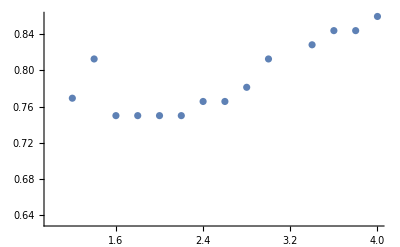

```mathematica
b3={{1,(65-27-1)/64}, {1.2,(65-14-1)/65},{1.4,(65-12-1)/64},{1.6,(65-16-1)/64}, {1.8,(65-16-1)/64},{2,(65-16-1)/64},{2.2,(65-16-1)/64},{2.4,(65-15-1)/64},{2.6,(65-15-1)/64},{2.8,(65-14-1)/64},{3,(65-12-1)/64},{3.2,(65-30-1)/64},{3.4,(65-11-1)/64},{3.6,(65-10-1)/64},{3.8,(65-10-1)/64},{4,(65-9-1)/64}};
ListPlot[b3]
```

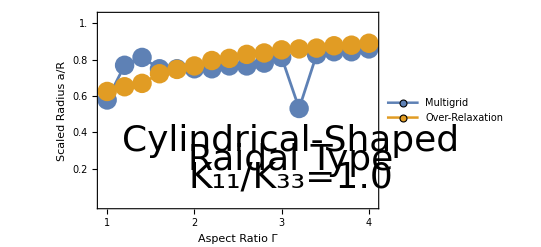

```mathematica
ListPlot[{b3,bb3},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.2,0.4,0.6,0.8,1.0},None},{{1,2,3,4},None}}, PlotRange->{{0.95,4.05},{0,1.04}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"Multigrid", "Over-Relaxation"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Bottom}],Epilog->{Text[Style["Cylindrical-Shaped",Directive[Black,36]],{3.1,0.35}],Text[Style["Raidal Type",Directive[Black,36]],{3.1,0.25}],Text[Style["K_11/K_33=1.0",Directive[Black,36]],{3.1,0.15}]}]
```

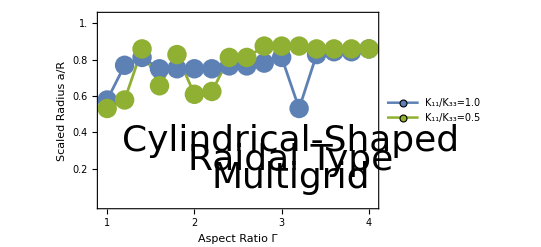

```mathematica
ListPlot[{b3,b},PlotStyle->{{Thickness[0.005],RGBColor[0.368417,0.506779,0.709798]},{Thickness[0.005],RGBColor[0.560181,0.691569,0.194885]}},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.2,0.4,0.6,0.8,1.0},None},{{1,2,3,4},None}}, PlotRange->{{0.95,4.05},{0,1.04}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=1.0", "K_11/K_33=0.5"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Bottom}],Epilog->{Text[Style["Cylindrical-Shaped",Directive[Black,36]],{3.1,0.35}],Text[Style["Raidal Type",Directive[Black,36]],{3.1,0.25}],Text[Style["Multigrid",Directive[Black,36]],{3.1,0.15}]}]
```

```mathematica
ColorData[97,"ColorList"]//InputForm
```

{RGBColor[0.368417, 0.506779, 0.709798], RGBColor[0.880722, 0.611041, 0.142051], RGBColor[0.560181, 0.691569, 0.194885], 
 RGBColor[0.922526, 0.385626, 0.209179], RGBColor[0.528488, 0.470624, 0.701351], RGBColor[0.772079, 0.431554, 0.102387], 
 RGBColor[0.363898, 0.618501, 0.782349], RGBColor[1, 0.75, 0], RGBColor[0.647624, 0.37816, 0.614037], 
 RGBColor[0.571589, 0.586483, 0.], RGBColor[0.915, 0.3325, 0.2125], RGBColor[0.40082222609352647, 0.5220066643438841, 0.85], 
 RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142], RGBColor[0.736782672705901, 0.358, 0.5030266573755369], 
 RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}